# Monitoring Rust deformation for Box_4E

## Setup

Set your environment variables below

```mathematica
LTDFolder = "/home/ben/Sync/Research/pyNLoop";
PythonInterpreter = "/usr/bin/python2";
CUBAPath = "/Users/valentin/Documents/HEP_softs/Cuba-4.2/lib";
TopologyName ="Box_4E_no_z_component_sources";
```

Then start the process hook to the Python bindings

```mathematica
GetLTDHook[topo_]:= StartProcess[{
PythonInterpreter,
LTDFolder<>"/"<>"get_deformation.py",
topo}
];

GetLTDEvaluationHook[topo_]:= StartProcess[{
PythonInterpreter,
LTDFolder<>"/"<>"get_evaluation.py",
topo}
];
```

We can now build a function using the hook to access the deformation

```mathematica
GetDeformationFromRust[hook_, RealMomenta_]:=Module[
{RawOutput, DeformedMomenta},
(*Print[RealMomenta];*)

(* Write the real momenta to sys.stdin of the hook *)

WriteLine[hook,
StringJoin[
Riffle[Table[
StringJoin[
Riffle[
Table[ToString[ke],{ke, k}],
" "]
],
{k,RealMomenta}
]," "]
]
];

(* Now recover the deformed momenta *)
RawOutput = ReadLine[hook];
(*Print[RawOutput];*)

(* Parse it *)
DeformedMomenta = Table[
Read[
If[ke=="nan",
Print["NaN from:"<>ToString[RealMomenta]];
StringToStream["0"],
StringToStream[ke]],
Number],{ke,StringSplit[RawOutput]}];

(* Reshape and return *)
ArrayReshape[DeformedMomenta,{Length[DeformedMomenta]/3,3}]
]

GetEvaluationFromRust[hook_, RealMomenta_]/;Element[RealMomenta,Reals]:=Module[
{RawOutput, DeformedMomenta},
(*Print[RealMomenta];*)

(* Write the real momenta to sys.stdin of the hook *)
WriteLine[hook,
StringJoin[
Riffle[Table[
StringJoin[
Riffle[
Table[ToString[NumberForm[ke,Infinity,ExponentFunction->(Null&)]],{ke, k}],
" "]
],
{k,RealMomenta}
]," "]
]
];

(* Now recover the deformed momenta *)
RawOutput = ReadLine[hook];
(*Print[RawOutput];*)

(* Parse it *)
DeformedMomenta = Table[
Read[
If[ke=="nan",
Print["NaN from:"<>ToString[RealMomenta]];
StringToStream["0"],
StringToStream[ke]],
Number],{ke,StringSplit[RawOutput]}];

DeformedMomenta
]
```

## Test it now!

```mathematica
(* Refresh the hook so as to make sure changes in the yaml file took effect. *)
LTDHook = GetLTDHook[TopologyName]
```

ProcessObject[…]

```mathematica
a =GetDeformationFromRust[LTDHook, {
  {1.,2.,0.}
  }]
```

{{0.455383,-1.21056,0.}}

```mathematica
LTDEvaluationHook = GetLTDEvaluationHook[TopologyName]
```

ProcessObject[…]

```mathematica
GetEvaluationFromRust[LTDEvaluationHook,{{1,2,0}}][[1]]
```

1.37134×10^-8

```mathematica
{1,2,3}5
Transpose[{{1,2},{3,4},{5,6}}]
```

{5,10,15}

{{1,3,5},{2,4,6}}

```mathematica
LTDEvaluationHook = GetLTDEvaluationHook[TopologyName];
t=Block[{mytable},
mytable=Transpose[Table[GetEvaluationFromRust[LTDEvaluationHook,{{41.4,-4.8,0.} +{-6.6,-40.0,0.}+ i{-1,0.55,0.}/10}], {i,-50,650}]];
mytable[[3]](*Table[t/ Median[Abs[t]] Length[t],{t,mytable}]*)
];
```

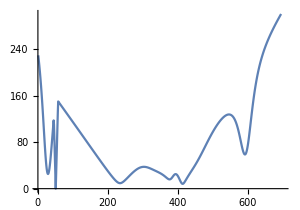

```mathematica
ListPlot[t,AspectRatio->0.7,Ticks->None,ImageSize->300,Joined->True,PlotRange->{Automatic,{0,30}}]
```

```mathematica
LTDEvaluationHook = GetLTDEvaluationHook[TopologyName];
t=Block[{mytable},
mytable=Transpose[Table[GetEvaluationFromRust[LTDEvaluationHook,{{41.4,-4.8,0.} +{-6.6,-40.0,0.}+ i{-1,0.55,0.}/100}], {i,-500,6500}]];
Table[t/ Median[Abs[t]] Length[t],{t,mytable}][[3]]
];
```

$Aborted

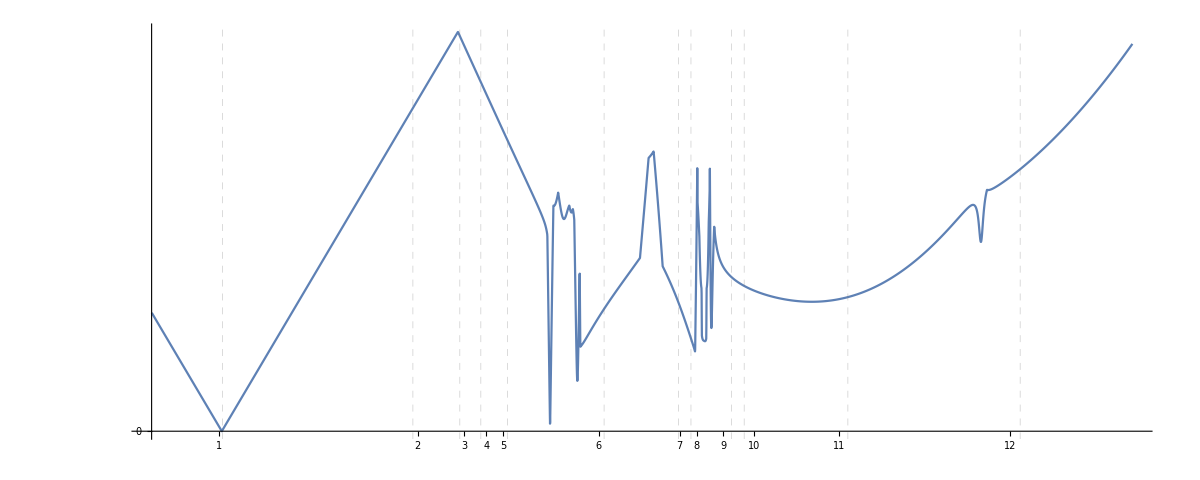

```mathematica
ListLinePlot[t,Ticks->{{{480,1, {0,0}},{1900,2, {0,0}},{2230,3, {0,0}},{2390,4, {0,0}},{2510,5, {0,0}},{3190,6, {0,0}},{3770,7, {0,0}},{3890,8, {0,0}},{4080,9, {0,0}},{4300,10, {0,0}},{4910,11, {0,0}},{6130,12, {0,0}}},{{0,0,{0,0}}}},GridLines->{{{505,Dashed},{1865,Dashed},{2200,Dashed},{2350,Dashed},{2540,Dashed},{3230,Dashed},{3760,Dashed},{3850,Dashed},{4140,Dashed},{4230,Dashed},{4970,Dashed},{6200,Dashed}},{}},
TicksStyle->Directive[FontSize->16],ImageSize->1200,AspectRatio->0.4]
(*ListLogPlot[Abs[Transpose[Table[GetEvaluationFromRust[LTDEvaluationHook,{{41.4,-4.8,0.} +{-6.6,-40.0,0.}+ i{-1,0.55,0.}/10}], {i,-50,650}]]],Joined->True,PlotLegends->{"Re", "Im", "|kappa|", "J_Re", "J_Im"}]*)
```

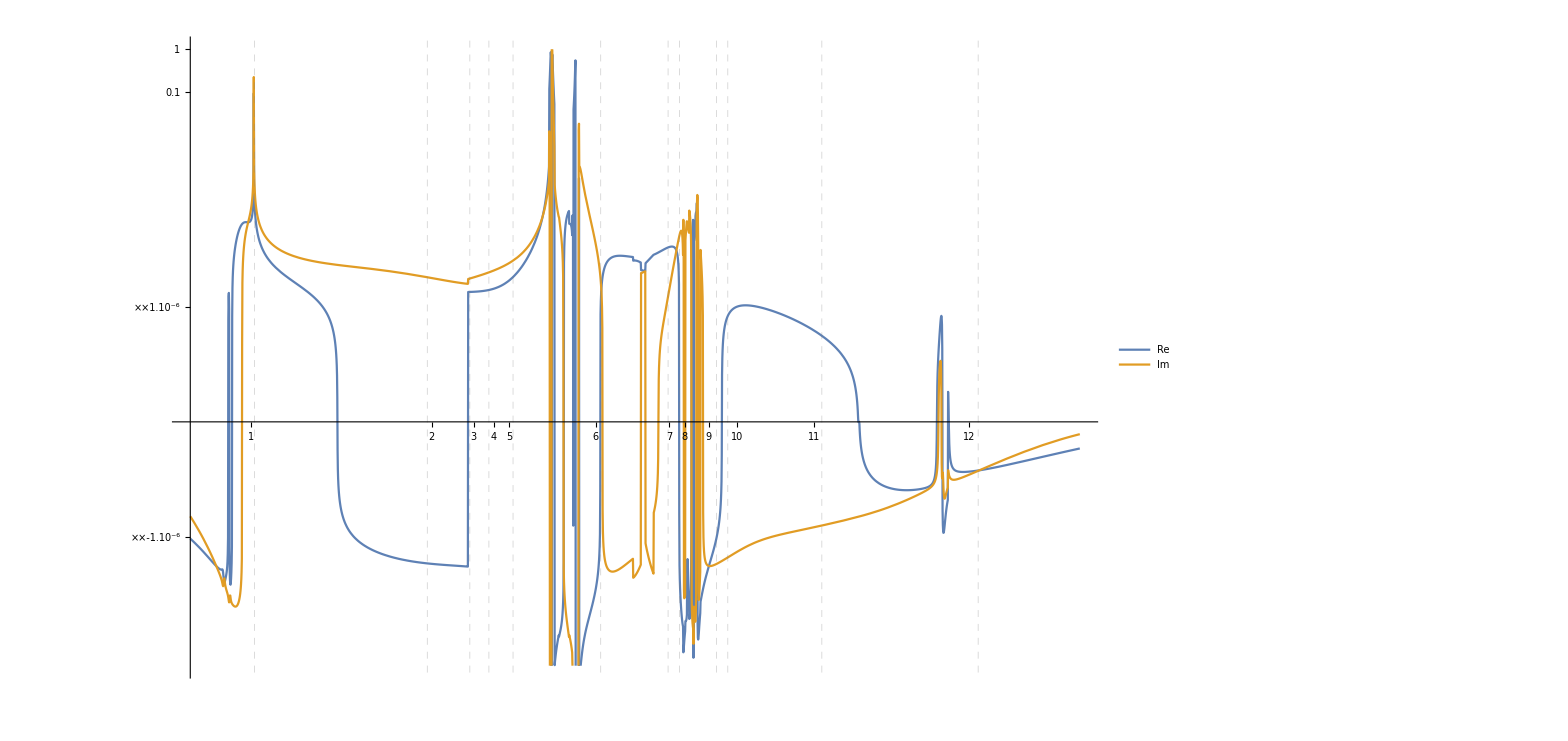

```mathematica
logify[off_][a_List]:=logify[off]/@a
logify[off_][x_?Positive]:=Max[0,(off+Re@Log@x)/off]
logify[off_][x_?Negative]:=Min[0,(off+Re@Log@x)/-off]

invlog[off_][a_List]:=invlog[off]/@a
invlog[off_][x_?Positive]:=Exp[x*off-off]
invlog[off_][x_?Negative]:=-Exp[-x*off-off]
LTDEvaluationHook = GetLTDEvaluationHook[TopologyName];
Block[{testre,testim,test,r},
testre[x_]:=GetEvaluationFromRust[LTDEvaluationHook,{{41.4,-4.8,0.} +{-6.6,-40.0,0.}+ (x-500){-1,0.55,0.}/100}][[1]];
testim[x_]:=GetEvaluationFromRust[LTDEvaluationHook,{{41.4,-4.8,0.} +{-6.6,-40.0,0.}+ (x-500){-1,0.55,0.}/100}][[2]];
Plot[{testre[x],testim[x]},{x,0,7000},PlotLegends->Placed[{"Re", "Im"},{0.95,0.8}],ScalingFunctions->{logify[20], invlog[20]}, PlotRange->{-0.001,1}, Ticks->{{{480,1, {0,0}},{1900,2, {0,0}},{2230,3, {0,0}},{2390,4, {0,0}},{2510,5, {0,0}},{3190,6, {0,0}},{3770,7, {0,0}},{3890,8, {0,0}},{4080,9, {0,0}},{4300,10, {0,0}},{4910,11, {0,0}},{6130,12, {0,0}}},Automatic},GridLines->{{{505,Dashed},{1865,Dashed},{2200,Dashed},{2350,Dashed},{2540,Dashed},{3230,Dashed},{3760,Dashed},{3850,Dashed},{4140,Dashed},{4230,Dashed},{4970,Dashed},{6200,Dashed}},{}},
TicksStyle->Directive[FontSize->16],ImageSize->1200]]
```

```mathematica
(*LTDEvaluationHook = GetLTDEvaluationHook[TopologyName];
dp=DensityPlot[Log[Abs[GetEvaluationFromRust[LTDEvaluationHook, {{kx,ky,0.0}-{6.6,40.0,0.0}}][[1]]]],{kx,-30,50},{ky,-20,50}, PlotPoints->50,Axes->False,
Frame->True,
ImagePadding->1]*)
```

$Aborted

$Aborted

```mathematica
(*dpim=DensityPlot[Log[Abs[GetEvaluationFromRust[LTDEvaluationHook, {{kx,ky,0.0}-{6.6,40.0,0.0}}][[2]]]],{kx,-30,50},{ky,-20,50}, PlotPoints->40,Axes->False,
Frame->True,
ImagePadding->1]*)
```

```mathematica
(*DumpSave["heatmap.mx", {dp,dpim}]*)
```

```mathematica
<< heatmap.mx
dp
```

$Aborted[]

$Failed

dp

## Apply it to Box_4E

Definition of the Box_4E integrand

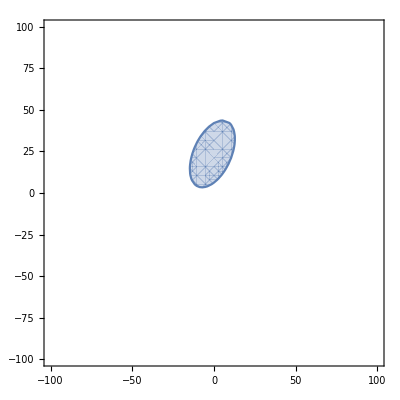
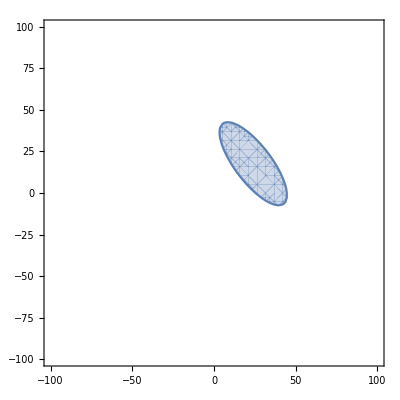
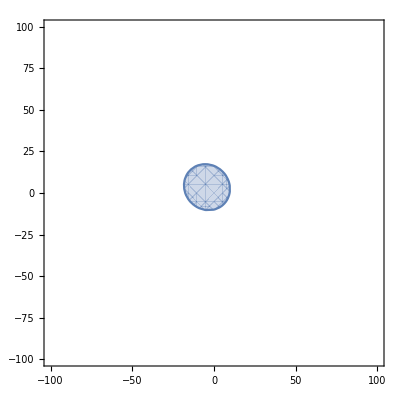
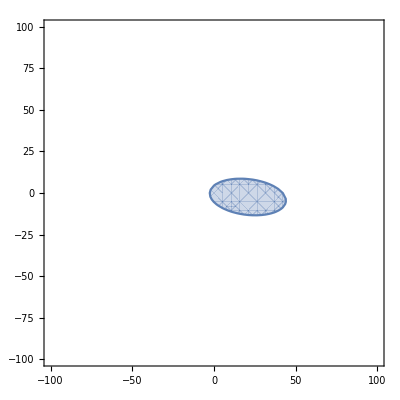
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{{1,2},{1,3},{1,4}},{{2,3},{2,4}},{{3,4}},{}}

```mathematica
Ellipsoids[k_,p_,m_,p0_,N_]:=Flatten[Table[{Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]+p0[[j]]-p0[[i]]<0, Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]-p0[[j]]+p0[[i]]<0},{i, 1,N},{j,i+1,N}]]
BoxIntegrand[k_, p1_,p2_,p3_,p01_,p02_,p03_]:=Ellipsoids[k,{p1,p1+p2,p1+p2+p3,0},{0,0,0,0},{p01,p01+p02,p01+p02+p03,0},4];
T[t_,M_]=t^2/(t^2+M^2);

integrandsIneq=BoxIntegrand[{kx,ky},{-6.6,-40.0},{15.2,33},{-50,11.8},14, -43,-17.9];
integrands = integrandsIneq/.{x_<0->x};
integrandsIneqBound=BoxIntegrand[{kx,ky},{-6.6,-40.0},{15.2,33},{-50,11.8},14/(1-0.3^2), -43/(1-0.3^2),-17.9/(1-0.3^2)];
Table[RegionPlot[ieq<0
,{kx,-100,100},{ky,-100,100}],{ieq,integrands}]
Table[{i,j},{i, 1,4},{j,i+1,4}]
```

```mathematica
existingEllipsoids={integrands[[1]],integrands[[3]],integrands[[10]],integrands[[12]]};
existingEllipsoids
```

{-43+√((-6.6+kx)^2+(-40.+ky)^2)+√((8.6+kx)^2+(-7.+ky)^2),-60.9+√((-6.6+kx)^2+(-40.+ky)^2)+√((-41.4+kx)^2+(4.8+ky)^2),-29+√((8.6+kx)^2+(-7.+ky)^2)+√(kx^2+ky^2),-46.9+√(kx^2+ky^2)+√((-41.4+kx)^2+(4.8+ky)^2)}

```mathematica
Table[RegionPlot[ieq<0
,{kx,-100,100},{ky,-100,100}],{ieq,existingEllipsoids}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

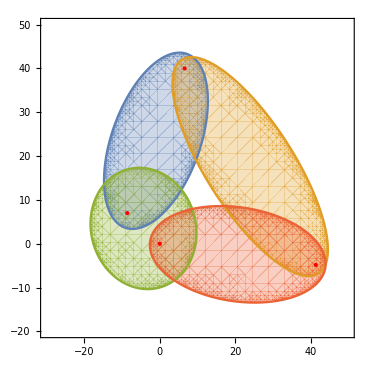

```mathematica
Show[RegionPlot[
{-43+√((-6.6+kx)^2+(-40.+ky)^2)+√((8.6+kx)^2+(-7.+ky)^2)<0,-60.9+√((-6.6+kx)^2+(-40.+ky)^2)+√((-41.4+kx)^2+(4.800000000000001+ky)^2)<0,-29+√((8.6+kx)^2+(-7.+ky)^2)+√(kx^2+ky^2)<0,-46.9+√(kx^2+ky^2)+√((-41.4+kx)^2+(4.800000000000001+ky)^2)<0}
,{kx,-30,50},{ky,-20,50},MaxRecursion->5
],Graphics[{PointSize[Large],Red,Point[{6.6,40}]}],
Graphics[{PointSize[Large],Red,Point[{-8.6,7}]}],
Graphics[{PointSize[Large],Red,Point[{41.4,-4.8}]}],
Graphics[{PointSize[Large],Red,Point[{0,0}]}]]
```

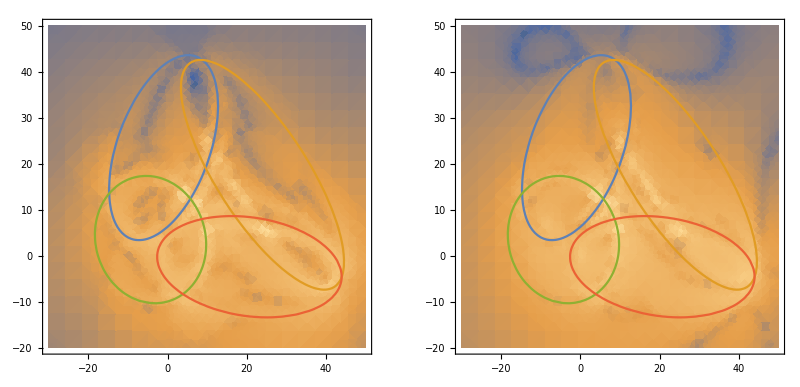

```mathematica
GraphicsRow[{Show[dp,ContourPlot[{integrands[[1]]==0,integrands[[3]]==0,integrands[[10]]==0,integrands[[12]]==0},{kx,-30,50},{ky,-20,50}]],
Show[dpim,ContourPlot[{integrands[[1]]==0,integrands[[3]]==0,integrands[[10]]==0,integrands[[12]]==0},{kx,-30,50},{ky,-20,50}]]}]
```

Access to Rust Vector Field, specialised to 2 dimensions

```mathematica
DeformationVector[kx_,ky_]/;Element[kx,Reals]/;Element[ky,Reals]:= GetDeformationFromRust[LTDHook, {{NumberForm[kx-6.6,Infinity,ExponentFunction->(Null&)],NumberForm[ky-40.0,Infinity,ExponentFunction->(Null&)],0.}}][[1]][[1;;2]]; (*note the shift *)
```

```mathematica
DeformedSurface[i_,kkx_,kky_]/;Element[kkx,Reals]/;Element[kky,Reals]:=Module[{kappas},
kappas=DeformationVector[kkx, kky];
(*Print["kappa",kappas];*)
Re[integrands[[i]] /.{kx->kkx + I kappas[[1]], ky->kky + I kappas[[2]]}]];
DeformedSurfaceIm[i_,kkx_,kky_]/;Element[kkx,Reals]/;Element[kky,Reals]:=Module[{kappas},
kappas=DeformationVector[kkx, kky];
(*Print["kappa",kappas];*)
Im[integrands[[i]] /.{kx->kkx + I kappas[[1]], ky->kky + I kappas[[2]]}]];
```

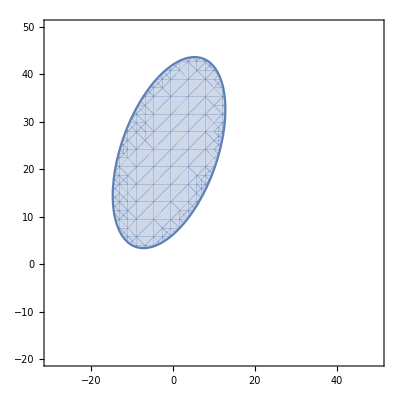
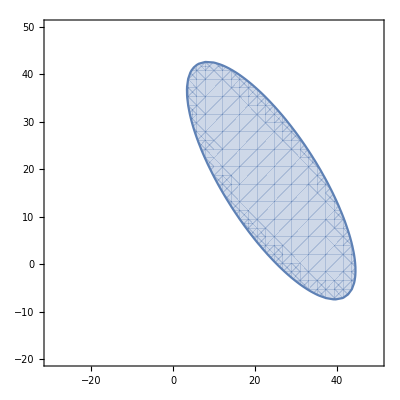
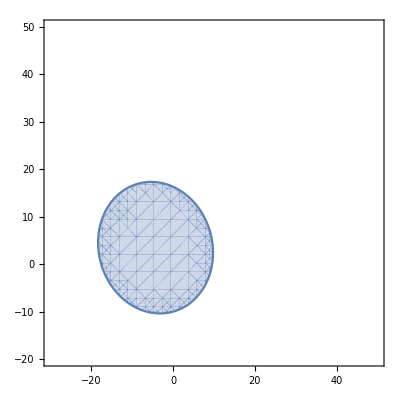
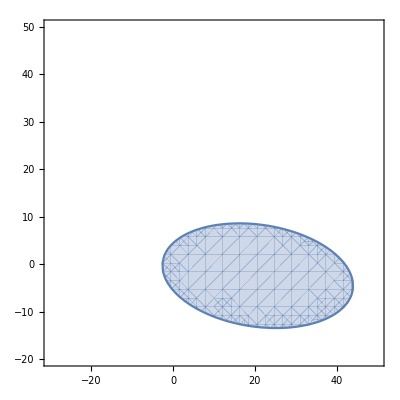

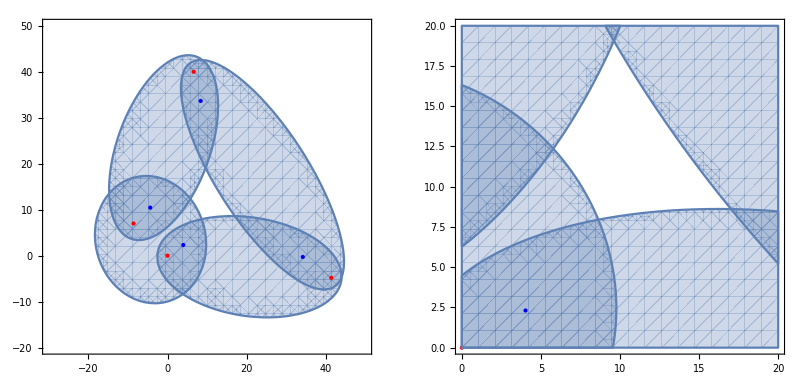

```mathematica
ellipsoids=RegionPlot[
#1<0
,{kx,-30,50},{ky,-20,50}
]&/@existingEllipsoids;

ellipsoids

ellipsoidszoom=RegionPlot[
#1<0(*Print[RealMomenta];*)
,{kx,0,20},{ky,0,20}
]&/@existingEllipsoids;
GraphicsRow[{Show[
ellipsoids,
 {
Graphics[{PointSize[Large],Blue,Point[{1.7753337683882497,-6.34420992878801}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{-10.98354824164586,-29.54587623647136}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{27.596641411742628,-40.27143847946829}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{-2.62336418048707,-37.6748195962582}-{-6.6,-40.0}]}],
(*4 foci*)
Graphics[{PointSize[Large],Red,Point[{6.6,40}]}],
Graphics[{PointSize[Large],Red,Point[{-8.6,7}]}],
Graphics[{PointSize[Large],Red,Point[{41.4,-4.8}]}],
Graphics[{PointSize[Large],Red,Point[{0,0}]}],
VectorPlot[
-DeformationVector[kx,ky]
,{kx,-30,50},{ky,-20,50},VectorPoints->35]}],
Show[
ellipsoidszoom,
 {
Graphics[{PointSize[Large],Blue,Point[{1.7753337683882497,-6.34420992878801}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{-10.98354824164586,-29.54587623647136}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{27.596641411742628,-40.27143847946829}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{-2.62336418048707,-37.6748195962582}-{-6.6,-40.0}]}],
(*4 foci*)
Graphics[{PointSize[Large],Red,Point[{6.6,40}]}],
Graphics[{PointSize[Large],Red,Point[{-8.6,7}]}],
Graphics[{PointSize[Large],Red,Point[{41.4,-4.8}]}],
Graphics[{PointSize[Large],Red,Point[{0,0}]}],
VectorPlot[
-DeformationVector[kx,ky]
,{kx,0,20},{ky,0,20},VectorPoints->35]}]}]
```

```mathematica
LTDHook =GetLTDHook[TopologyName];
ellipsoids:=Map[#<0&, existingEllipsoids];
ellipsoidsrender=RegionPlot[
ellipsoids
,{kx,-30,50},{ky,-20,50},
Axes->False,
Frame->True,
ImagePadding->1
];
ellipsoidsrenderzoom=RegionPlot[
ellipsoids
,{kx,0,20},{ky,0,20},
Axes->False,
Frame->True,
ImagePadding->1
];
```

```mathematica
<< defplot.mx
(*deformedsurfaces =ContourPlot[
{DeformedSurface[1,kkx,kky]==0,
DeformedSurface[3,kkx,kky]==0,
DeformedSurface[10,kkx,kky]==0,
DeformedSurface[12,kkx,kky]==0}
,{kkx,-30,50},{kky,-20,50}
];

deformedsurfacesim =ContourPlot[
{DeformedSurfaceIm[1,kkx,kky]==0,
DeformedSurfaceIm[3,kkx,kky]==0,
DeformedSurfaceIm[10,kkx,kky]==0,
DeformedSurfaceIm[12,kkx,kky]==0}
,{kkx,-30,50},{kky,-20,50},
ContourStyle->Dashed
]];
DumpSave["defplot.mx",{deformedsurfaces,deformedsurfacesim}];*)
```

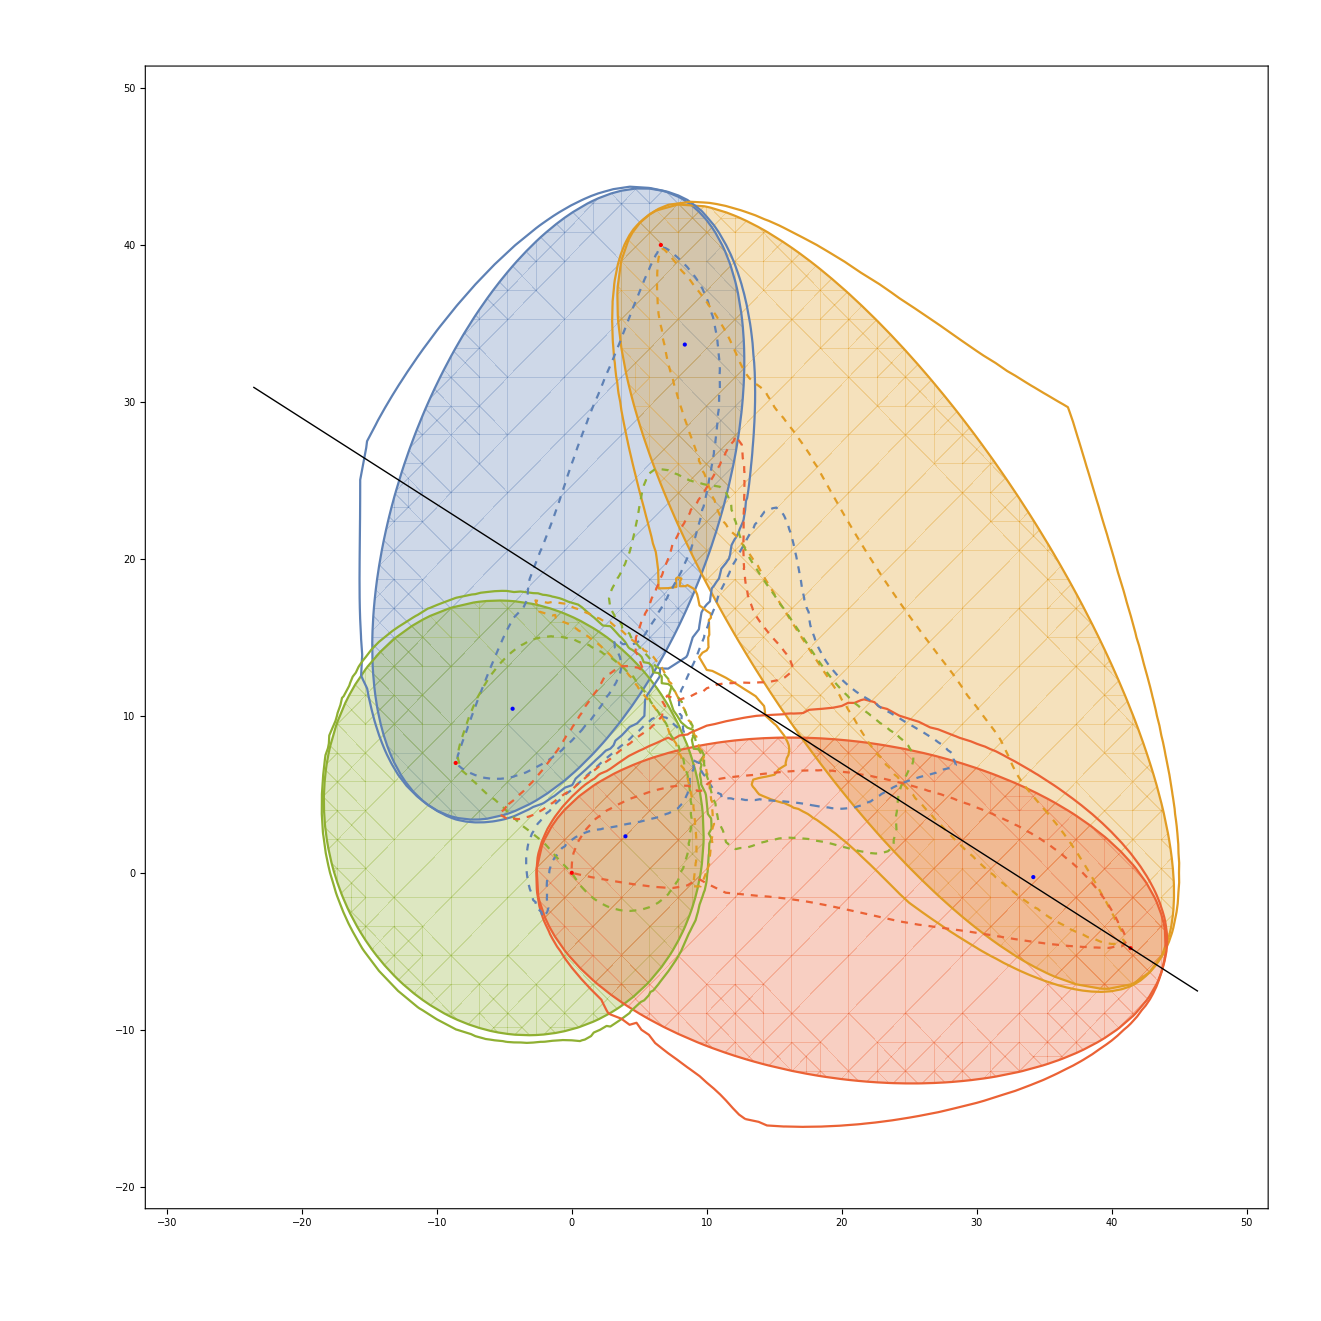

```mathematica
Show[
ellipsoidsrender,
deformedsurfaces ,
deformedsurfacesim,
{Graphics[{PointSize[Large],Blue,Point[{1.7753337683882497,-6.34420992878801}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{-10.98354824164586,-29.54587623647136}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{27.596641411742628,-40.27143847946829}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{-2.62336418048707,-37.6748195962582}-{-6.6,-40.0}]}],
(*4 foci*)
Graphics[{PointSize[Large],Red,Point[{6.6,40}]}],
Graphics[{PointSize[Large],Red,Point[{-8.6,7}]}],
Graphics[{PointSize[Large],Red,Point[{41.4,-4.8}]}],
Graphics[{PointSize[Large],Red,Point[{0,0}]}]
(*VectorPlot[
-DeformationVector[kx,ky]
,{kx,-30,50},{ky,-20,50},VectorPoints->35],*)
},
ListLinePlot[Table[Tooltip[{41.4,-4.8} + i{-1,0.55}/10,i+50], {i,-50,650}],PlotStyle->{Thick,Black}]]
```

```mathematica
<< defplotcolor.mx
deformedsurfacesc =ContourPlot[
{DeformedSurface[1,kkx,kky]==0,
DeformedSurface[3,kkx,kky]==0,
DeformedSurface[10,kkx,kky]==0,
DeformedSurface[12,kkx,kky]==0}
,{kkx,-30,50},{kky,-20,50},
ContourStyle->{{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.368417, 0.506779, 0.709798]]},{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.528488, 0.470624, 0.701351]]},{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.560181, 0.691569, 0.194885]]},{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.922526, 0.385626, 0.209179]]}}
]

deformedsurfacesimc =ContourPlot[
{DeformedSurfaceIm[1,kkx,kky]==0,
DeformedSurfaceIm[3,kkx,kky]==0,
DeformedSurfaceIm[10,kkx,kky]==0,
DeformedSurfaceIm[12,kkx,kky]==0}
,{kkx,-30,50},{kky,-20,50},
ContourStyle->{Directive[Dashed,AbsoluteThickness[0.0],RGBColor[0.368417, 0.506779, 0.709798]],Directive[Dashed,AbsoluteThickness[0.0],RGBColor[0.528488, 0.470624, 0.701351]],Directive[Dashed,AbsoluteThickness[0.0],RGBColor[0.560181, 0.691569, 0.194885]],Directive[Dashed,AbsoluteThickness[0.0],RGBColor[0.922526, 0.385626, 0.209179]]}
]
DumpSave["defplotcolor.mx",{deformedsurfacesc,deformedsurfacesimc}];
```

BinaryWrite::errfile: Could not access file File write failed.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

Table::iterb: Iterator {ke,StringSplit[EndOfFile]} does not have appropriate bounds.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

BinaryWrite::errfile: Could not access file File write failed.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

Table::iterb: Iterator {ke,StringSplit[EndOfFile]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

BinaryWrite::errfile: Could not access file File write failed.

General::stop: Further output of BinaryWrite::errfile will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Read::stream will be suppressed during this calculation.

-Graphics-

BinaryWrite::errfile: Could not access file File write failed.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

Table::iterb: Iterator {ke,StringSplit[EndOfFile]} does not have appropriate bounds.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

BinaryWrite::errfile: Could not access file File write failed.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

Table::iterb: Iterator {ke,StringSplit[EndOfFile]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

BinaryWrite::errfile: Could not access file File write failed.

General::stop: Further output of BinaryWrite::errfile will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Read::stream will be suppressed during this calculation.

-Graphics-

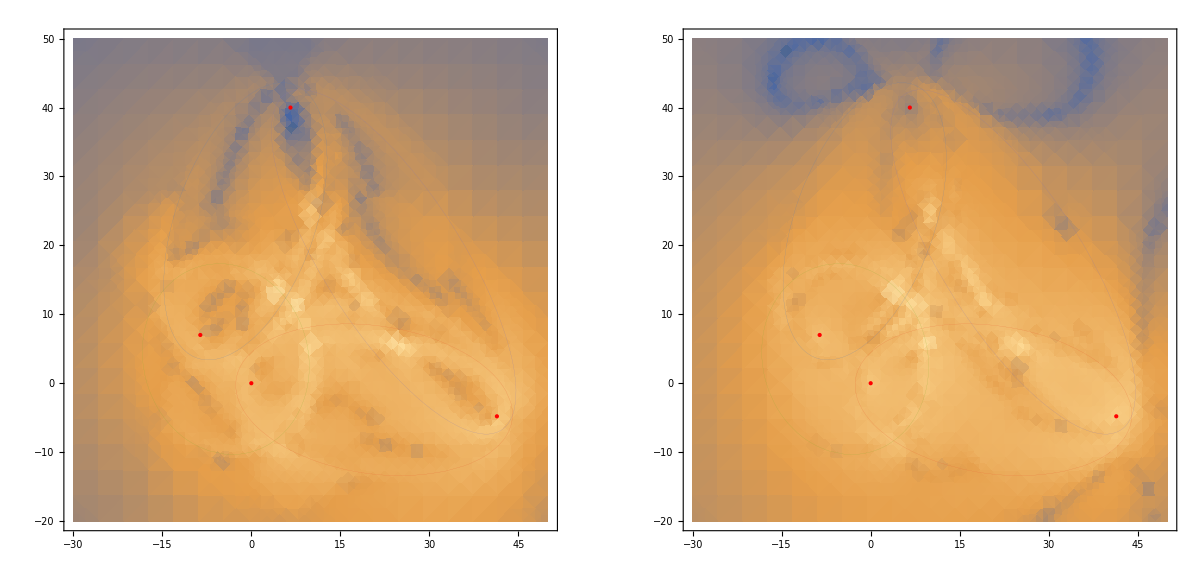

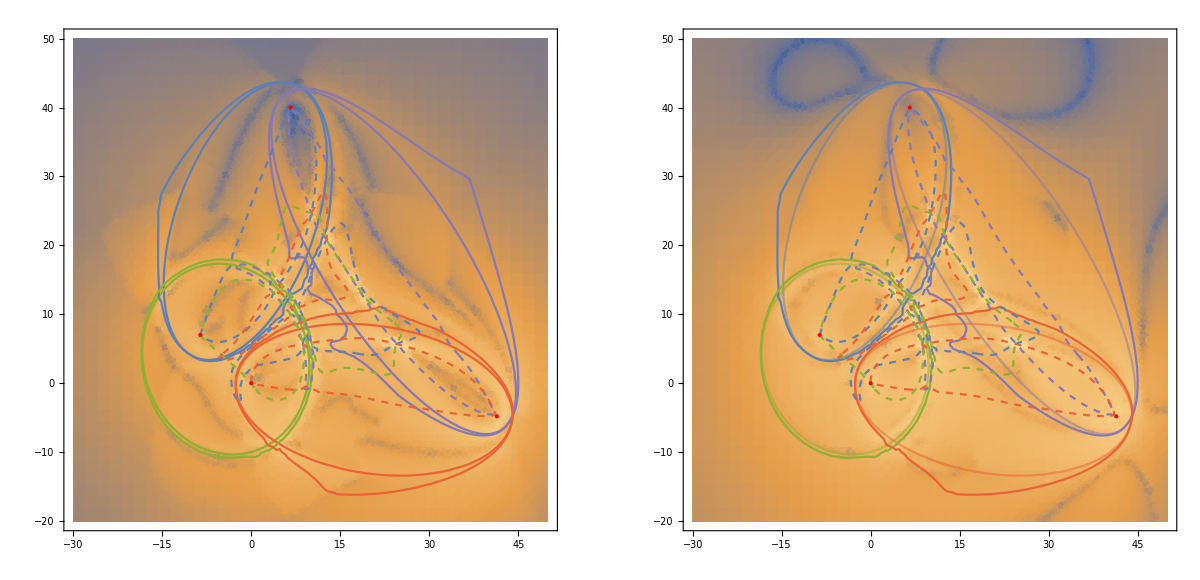

```mathematica
GraphicsRow[{Show[
dp,
ContourPlot[{integrands[[1]]==0,integrands[[3]]==0,integrands[[10]]==0,integrands[[12]]==0},{kx,-30,50},{ky,-20,50},ContourStyle->{{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.368417, 0.506779, 0.709798]]},{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.528488, 0.470624, 0.701351]]},{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.560181, 0.691569, 0.194885]]},{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.922526, 0.385626, 0.209179]]}}],
deformedsurfacesc,
deformedsurfacesimc,
{
(*4 foci*)
Graphics[{PointSize[Large],Red,Point[{6.6,40}]}],
Graphics[{PointSize[Large],Red,Point[{-8.6,7}]}],
Graphics[{PointSize[Large],Red,Point[{41.4,-4.8}]}],
Graphics[{PointSize[Large],Red,Point[{0,0}]}]
}
],
Show[
dpim,
ContourPlot[{integrands[[1]]==0,integrands[[3]]==0,integrands[[10]]==0,integrands[[12]]==0},{kx,-30,50},{ky,-20,50},ContourShading->False,ContourStyle->{{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.368417, 0.506779, 0.709798]]},{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.528488, 0.470624, 0.701351]]},{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.560181, 0.691569, 0.194885]]},{AbsoluteThickness[0.0],Opacity[1.0,RGBColor[0.922526, 0.385626, 0.209179]]}}],
deformedsurfacesc,
deformedsurfacesimc,
{
(*4 foci*)
Graphics[{PointSize[Large],Red,Point[{6.6,40}]}],
Graphics[{PointSize[Large],Red,Point[{-8.6,7}]}],
Graphics[{PointSize[Large],Red,Point[{41.4,-4.8}]}],
Graphics[{PointSize[Large],Red,Point[{0,0}]}]
}
]},
ImageSize->1200
]
```

```mathematica
<<defplotzoom.mx
```

```mathematica
(*
deformedsurfaceszoom =ContourPlot[
{DeformedSurface[1,kkx,kky]==0,
DeformedSurface[3,kkx,kky]==0,
DeformedSurface[10,kkx,kky]==0,
DeformedSurface[12,kkx,kky]==0}
,{kkx,0,20},{kky,0,20}
];deformedsurfacesimzoom =ContourPlot[
{DeformedSurfaceIm[1,kkx,kky]==0,
DeformedSurfaceIm[3,kkx,kky]==0,
DeformedSurfaceIm[10,kkx,kky]==0,
DeformedSurfaceIm[12,kkx,kky]==0}
,{kkx,0,20},{kky,0,20},
ContourStyle->Dashed
];
DumpSave["defplotzoom.mx",{deformedsurfaceszoom,deformedsurfacesimzoom}];*)
```

BinaryWrite::errfile: Could not access file File write failed.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

Table::iterb: Iterator {ke,StringSplit[EndOfFile]} does not have appropriate bounds.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

BinaryWrite::errfile: Could not access file File write failed.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

Table::iterb: Iterator {ke,StringSplit[EndOfFile]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

BinaryWrite::errfile: Could not access file File write failed.

General::stop: Further output of BinaryWrite::errfile will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

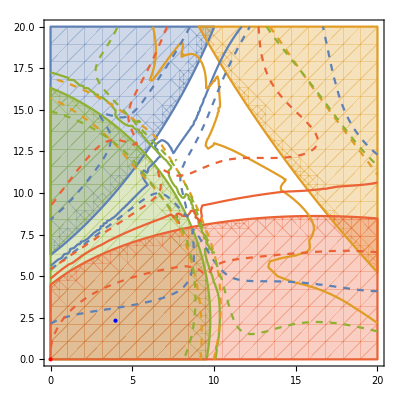

```mathematica
Show[
ellipsoidsrenderzoom,
deformedsurfaceszoom,
deformedsurfacesimzoom,
{Graphics[{PointSize[Large],Blue,Point[{1.7753337683882497,-6.34420992878801}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{-10.98354824164586,-29.54587623647136}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{27.596641411742628,-40.27143847946829}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{-2.62336418048707,-37.6748195962582}-{-6.6,-40.0}]}],
(*4 foci*)
Graphics[{PointSize[Large],Red,Point[{6.6,40}]}],
Graphics[{PointSize[Large],Red,Point[{-8.6,7}]}],
Graphics[{PointSize[Large],Red,Point[{41.4,-4.8}]}],
Graphics[{PointSize[Large],Red,Point[{0,0}]}],
VectorPlot[
-DeformationVector[kx,ky]
,{kx,0,20},{ky,0,20},VectorPoints->35]}]
```

```mathematica
backdrop={Graphics[{PointSize[Large],Blue,Point[{1.7753337683882497,-6.34420992878801}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{-10.98354824164586,-29.54587623647136}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{27.596641411742628,-40.27143847946829}-{-6.6,-40.0}]}],
Graphics[{PointSize[Large],Blue,Point[{-2.62336418048707,-37.6748195962582}-{-6.6,-40.0}]}],
(*4 foci*)
Graphics[{PointSize[Large],Red,Point[{6.6,40}]}],
Graphics[{PointSize[Large],Red,Point[{-8.6,7}]}],
Graphics[{PointSize[Large],Red,Point[{41.4,-4.8}]}],
Graphics[{PointSize[Large],Red,Point[{0,0}]}](*,
VectorPlot[
-DeformationVector[kx,ky]
,{kx,-30,50},{ky,-20,50},VectorPoints->35]*)
};
```

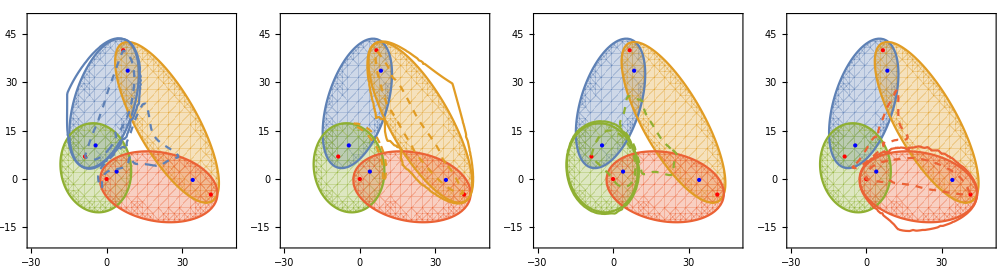

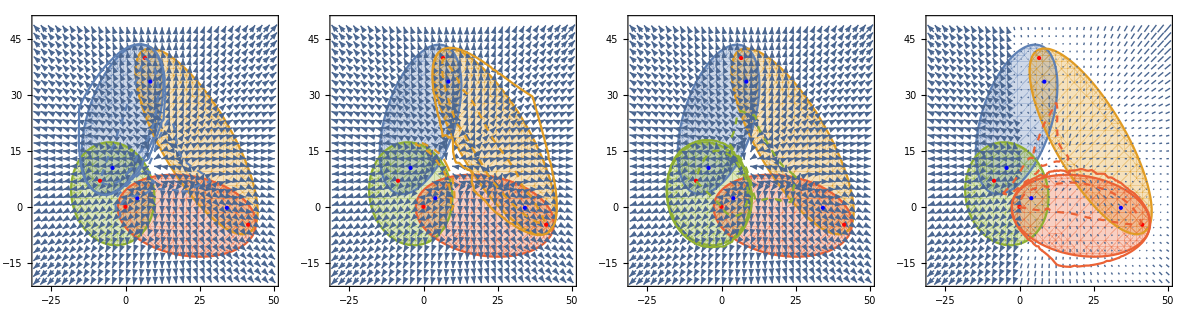

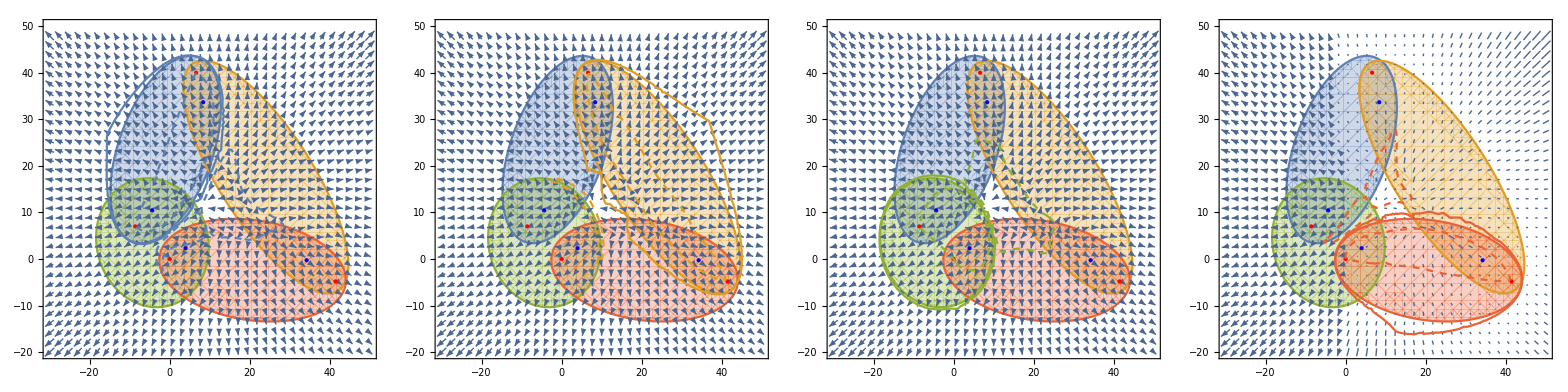

```mathematica
(*graphicrow={Show[
ellipsoidsrender,
backdrop,
ContourPlot[
{DeformedSurfaceIm[1,kkx,kky]==0, DeformedSurface[1,kkx,kky]==0}
,{kkx,-30,50},{kky,-20,50},
ContourStyle->{Directive[Dashed,ColorData[97,"ColorList"][[1]]], Directive[ColorData[97,"ColorList"][[1]]]}
]
],
Show[
ellipsoidsrender,
backdrop,
ContourPlot[
{DeformedSurfaceIm[3,kkx,kky]==0, DeformedSurface[3,kkx,kky]==0}
,{kkx,-30,50},{kky,-20,50},
ContourStyle->{Directive[Dashed,ColorData[97,"ColorList"][[2]]], Directive[ColorData[97,"ColorList"][[2]]]}
]
],
Show[
ellipsoidsrender,
backdrop,
ContourPlot[
{DeformedSurfaceIm[10,kkx,kky]==0, DeformedSurface[10,kkx,kky]==0}
,{kkx,-30,50},{kky,-20,50},
ContourStyle->{Directive[Dashed,ColorData[97,"ColorList"][[3]]], Directive[ColorData[97,"ColorList"][[3]]]}
]
],
Show[
ellipsoidsrender,
backdrop,
ContourPlot[
{DeformedSurfaceIm[12,kkx,kky]==0, DeformedSurface[12,kkx,kky]==0}
,{kkx,-30,50},{kky,-20,50},
ContourStyle->{Directive[Dashed,ColorData[97,"ColorList"][[4]]], Directive[ColorData[97,"ColorList"][[4]]]}
]
]
}
GraphicsRow[graphicrow,10]*)
```

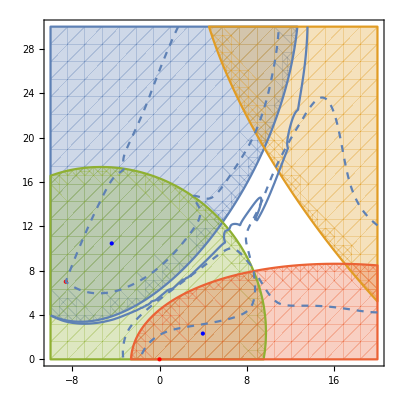

```mathematica
LTDHook =GetLTDHook[TopologyName];
elz=RegionPlot[
ellipsoids
,{kx,-10,20},{ky,0,30},
Axes->False,
Frame->True,
ImagePadding->1
];
badpole=Show[
elz,
backdrop,
ContourPlot[
{DeformedSurfaceIm[1,kkx,kky]==0, DeformedSurface[1,kkx,kky]==0}
,{kkx,-10,20},{kky,0,30},
MaxRecursion->4,
ContourStyle->{Directive[Dashed,ColorData[97,"ColorList"][[1]]], Directive[ColorData[97,"ColorList"][[1]]]}
]
]
```

BinaryWrite::errfile: Could not access file File write failed.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

Table::iterb: Iterator {ke,StringSplit[EndOfFile]} does not have appropriate bounds.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

BinaryWrite::errfile: Could not access file File write failed.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

Table::iterb: Iterator {ke,StringSplit[EndOfFile]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

BinaryWrite::errfile: Could not access file File write failed.

General::stop: Further output of BinaryWrite::errfile will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Read::stream will be suppressed during this calculation.

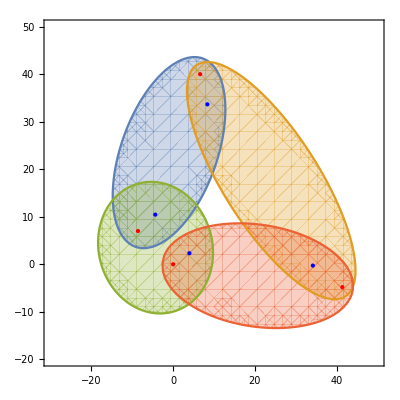

```mathematica
LTDHook =GetLTDHook[TopologyName];
goodpole=Show[
ellipsoidsrender,
backdrop,
ContourPlot[
{DeformedSurfaceIm[1,kkx,kky]==0, DeformedSurface[1,kkx,kky]==0}
,{kkx,-30,50},{kky,-20,50},
ContourStyle->{Directive[Dashed,ColorData[97,"ColorList"][[1]]], Directive[ColorData[97,"ColorList"][[1]]]}
]
]
```

```mathematica
LTDHook =GetLTDHook[TopologyName];
cp12 =ContourPlot[
DeformedSurface[12,kkx,kky]==0
,{kkx,-10,50},{kky,-25,25}
];
```

BinaryWrite::errfile: Could not access file File write failed.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

Table::iterb: Iterator {ke,StringSplit[EndOfFile]} does not have appropriate bounds.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

BinaryWrite::errfile: Could not access file File write failed.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

Table::iterb: Iterator {ke,StringSplit[EndOfFile]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

BinaryWrite::errfile: Could not access file File write failed.

General::stop: Further output of BinaryWrite::errfile will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[EndOfFile].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Read[If[ke==nan,Print[NaN from:<>ToString[«1»]];StringToStream[0],StringToStream[ke]],Number],{ke,StringSplit[EndOfFile]}],{2/3,3}].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

Read::stream: If[ke==nan,Print[NaN from:<>ToString[{{«3»,«3»,0.}}]];StringToStream[0],StringToStream[ke]] is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Read::stream will be suppressed during this calculation.

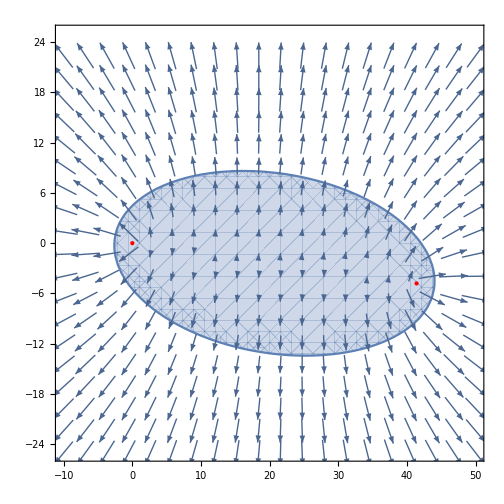

```mathematica
Show[
RegionPlot[
ellipsoids[[4]],{kx,-10,50},{ky,-25,25},
Axes->False,
Frame->True,
ImagePadding->1
],
cp12,
Graphics[{PointSize[Large],Red,Point[{41.4,-4.8}]}],
Graphics[{PointSize[Large],Red,Point[{0,0}]}],
VectorPlot[{kx-41.4,ky+4.8}/Sqrt[{kx-41.4,ky+4.8}.{kx-41.4,ky+4.8}]+{kx,ky}/Sqrt[{kx,ky}.{kx,ky}],{kx,-10,50},{ky,-25,25},VectorPoints->20]]
```

```mathematica
ellipsoids[[4]]
```

-46.9+√(kx^2+ky^2)+√((-41.4+kx)^2+(4.8+ky)^2)<0